Here we will derive the similar coefficient relation but now for the case that the series is:

This in turn means that the  will equal to

Then realize that:

Moreover, using Einstein notation realize that:

Then next define  which makes the above equal to:

Hence, for fixed i and j we have that:

```mathematica
CoeffSeriesPerGaus[v_,a_]:=Module[ {c=Table[If[i==1,Join[v,ConstantArray[0,Length[v]]][[j]],0],{i,1,2*Length[v]},{j,1,2*Length[v]}]}, Do[c[[i,j]]= If[i==1, Join[v,ConstantArray[0,Length[v]]][[j]]*(j-1)!, 1/(2*a)*(If[j+2>2*Length[v]||i-1<=0,0,c[[i-1,j+2]]]+Sum[Binomial[i-2,ip-1]*Binomial[j-1,jp-1]*If[jp+1>2*Length[v]||ip<=0,0,c[[ip,jp+1]]]*If[i-ip<=0||j-jp+2>2*Length[v],0,c[[i-ip,j-jp+2]]],{ip,1,i-1},{jp,1,j}])],{i,1,2*Length[v]},{j,1,2*Length[v]}];c]
```

```mathematica
Plotcoeffs[C_]:= Module[{dim ,rows,cols},dim = Dimensions[C]; rows= dim[[1]];cols=dim[[2]];
Graphic= Graphics[Table[{If[C[[x,y]]==0,Black,White],Rectangle[{x-1.5,y-1.5},{x-0.5,y-0.5}]},{x,1,rows},{y,1,cols}],Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{{"j: power of x",None},{"i: power of λ", None}},FrameTicks->All, PlotRange->{{-0.5,cols-0.5},{-0.5,rows-0.5}}, ImageSize->300]; Graphic]
```

```mathematica
𝔼/:𝔼[A_]×𝔼[B_]:=𝔼[A+B];
𝔼/:𝔼[0]:=1;
```

```mathematica
ObtGInt[v_, a_]:= Module[{C, dim ,rows,cols, Z}, C= CoeffSeriesPerGaus[v, a]; dim = Dimensions[C]; rows= dim[[1]];cols=dim[[2]];
Z= Sum[1/ ((i-1)! *(j-1)!)* C[[i,j]] * λ^(i-1)*x^(j-1),{i,1,rows}, {j,1,cols}]; Sqrt[2*Pi]*a^(-1/2)*𝔼[Z/.λ->1/.Thread[x->0]]]
```

## Coefficients plots

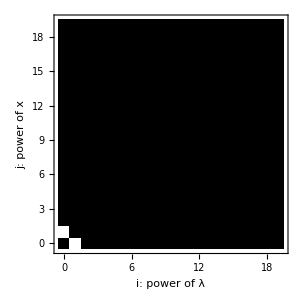

```mathematica
CL1 = CoeffSeriesPerGaus[{0,1,0,0,0,0,0,0,0,0},1];
Plotcoeffs[CL1]
```

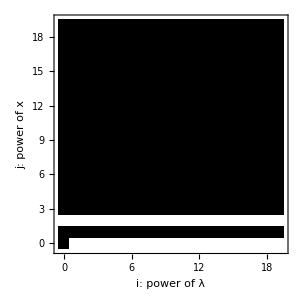

```mathematica
CL2 = CoeffSeriesPerGaus[{0,0,1,0,0,0,0,0,0,0},1];
Plotcoeffs[CL2]
```

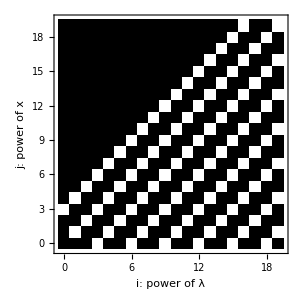

```mathematica
CL3 = CoeffSeriesPerGaus[{0,0,0,1,0,0,0,0,0,0},1];
Plotcoeffs[CL3]
```

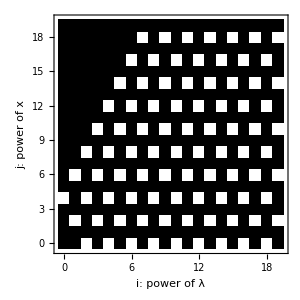

```mathematica
CL4 = CoeffSeriesPerGaus[{0,0,0,0,1,0,0,0,0,0},1];
Plotcoeffs[CL4]
```

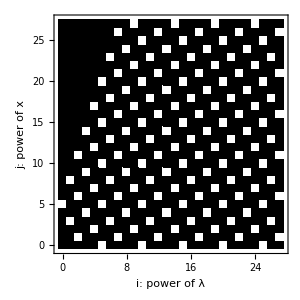

```mathematica
CL5 = CoeffSeriesPerGaus[{0,0,0,0,0,1,0,0,0,0,0,0,0,0},1];
Plotcoeffs[CL5]
```

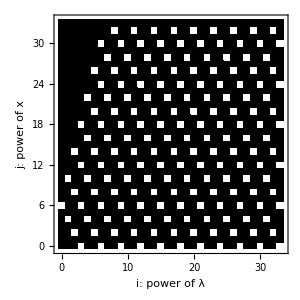

```mathematica
CL6 = CoeffSeriesPerGaus[{0,0,0,0,0,0,1,0,0,0,0,0,0,0, 0, 0, 0},1];
Plotcoeffs[CL6]
```

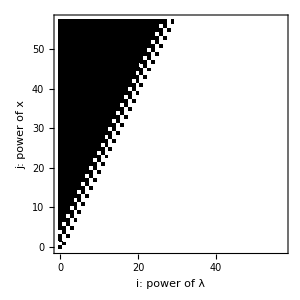

```mathematica
CLbaby = CoeffSeriesPerGaus[{0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},1];
Plotcoeffs[CLbaby]
```

```mathematica
ObtGIntSimpel[v_, a_]:= Module[{C, dim ,rows,cols, Z}, C= CoeffSeriesPerGaus[v, a]; dim = Dimensions[C]; rows= dim[[1]];cols=dim[[2]];
Z= Sum[1/ ((i-1)! *(j-1)!)* C[[i,j]] * λ^(i-1)*x^(j-1),{i,1,rows}, {j,1,cols}];  Sqrt[2*Pi]*a^(-1/2)*𝔼[Collect[FullSimplify[Z/.λ->1/.Thread[x->0]],ϵ]]]
```

## Comparing to P-code

```mathematica
ObtGInt[{0,0,b,0,0,0}, a] (*Disagrees with correct value*)
```

1/(√a)√(2 π) 𝔼[b/a+b^2/a^2+(4 b^3)/(3 a^3)+(2 b^4)/a^4+(16 b^5)/(5 a^5)+(16 b^6)/(3 a^6)+(64 b^7)/(7 a^7)+(16 b^8)/a^8+(256 b^9)/(9 a^9)+(256 b^10)/(5 a^10)+(1024 b^11)/(11 a^11)]

```mathematica
ObtGInt[{0,0,0,0}, a - 2*b] (*Agrees*)
```

(√(2 π))/(√(a-2 b))

```mathematica
ObtGInt[{0,0,0,b,0,0,0,0}, a] (*Agrees*)
```

(√(2 π) 𝔼[(15 b^2)/(2 a^3)+(405 b^4)/a^6+(89505 b^6)/(2 a^9)+(7413930 b^8)/a^12+(1630244475 b^10)/a^15])/(√a)

```mathematica
ObtGInt[{0,0,0,0,b,0,0,0}, a] (*Agrees except the last coefficient*)
```

1/(√a)√(2 π) 𝔼[(3 b)/a^2+(48 b^2)/a^4+(1584 b^3)/a^6+(78336 b^4)/a^8+(25671168 b^5)/(5 a^10)+(418185216 b^6)/a^12+(247301517312 b^7)/(7 a^14)]

```mathematica
ObtGInt[{0,0,0,0,0,b,0,0}, a](*Agrees except the last coefficient*)
```

(√(2 π) 𝔼[(945 b^2)/(2 a^5)+(27168750 b^4)/a^10+(3181655531250 b^6)/a^15])/(√a)

```mathematica
ObtGInt[{0,0,0,0,0,0,b,0}, a](*Agrees except the last two coefficients*)
```

(√(2 π) 𝔼[(15 b)/a^3+(5085 b^2)/a^6+(5666400 b^3)/a^9+(6374367900 b^4)/a^12+(6940244851200 b^5)/a^15])/(√a)

## Testing out Integration Properties

Fubini - Comparing with P-code

```mathematica
ObtGIntSimpel[{-c*y^2/2 + ξ2*y,-b*y +  ξ1,0,0}, a]
```

ObtGIntSimpel[{-(c y^2)/2+y ξ2,-b y+ξ1,0,0},a]

```mathematica
ObtGIntSimpel[{ξ1^2/(2*a), 0-ξ1*b/a + ξ2,0,0,0},c-b^2/a]
```

ObtGIntSimpel[{ξ1^2/(2 a),-(b ξ1)/a+ξ2,0,0,0},-b^2/a+c]

```mathematica
ObtGIntSimpel[{-c*y^2/2 + ξ2*y^2,-b*y ,0,0}, a-2*ξ1]
```

ObtGIntSimpel[{-(c y^2)/2+y^2 ξ2,-b y,0,0},a-2 ξ1]

```mathematica
ObtGIntSimpel[{0,0 ,0,0}, c-2*ξ2 -b^2 / (a - 2*ξ1)]
```

ObtGIntSimpel[{0,0,0,0},c-b^2/(a-2 ξ1)-2 ξ2]

```mathematica
ObtGIntSimpel[{-c*y^2/2 ,(ξ-b)*y ,0,0}, a]
```

ObtGIntSimpel[{-(c y^2)/2,y (-b+ξ),0,0},a]

```mathematica
ObtGIntSimpel[{0,0,0,0}, -((b-ξ)^2-ac)/(a)]
```

ObtGIntSimpel[{0,0,0,0},(ac-(b-ξ)^2)/a]

```mathematica
ObtGIntSimpel[{-c*y^2/2 + ξ4*y^2+ ξ2*y,ξ1-b*y ,0,0}, a-2*ξ3]
```

ObtGIntSimpel[{-(c y^2)/2+y ξ2+y^2 ξ4,-b y+ξ1,0,0},a-2 ξ3]

```mathematica
ObtGIntSimpel[{ ξ1^2/( 2*(a - 2*ξ3)), ξ2- b*ξ1/ (a - 2*ξ3),0,0}, c-2*ξ4 -b^2 / (a - 2*ξ3)]
```

ObtGIntSimpel[{ξ1^2/(2 (a-2 ξ3)),ξ2-(b ξ1)/(a-2 ξ3),0,0},c-b^2/(a-2 ξ3)-2 ξ4]

## Testing out 0-dimensional QFT examples

```mathematica
ObtGIntSimpel[{0,J,0,0,-ϵ/24,0,0, 0,0}, m^2]
```

1/(√(m^2))√(2 π) 𝔼[J^2/(2 m^2)-((J^4+6 J^2 m^2+3 m^4) ϵ)/(24 m^8)+((2 J^6+21 J^4 m^2+48 J^2 m^4+12 m^6) ϵ^2)/(144 m^14)-((2 J^8+32 J^6 m^2+149 J^4 m^4+198 J^2 m^6+33 m^8) ϵ^3)/(288 m^20)+((44 J^10+981 J^8 m^2+7368 J^6 m^4+21276 J^4 m^6+19584 J^2 m^8+2448 m^10) ϵ^4)/(10368 m^26)-((455 J^12+13326 J^10 m^2+143685 J^8 m^4+691740 J^6 m^6+1431450 J^4 m^8+1002780 J^2 m^10+100278 m^12) ϵ^5)/(155520 m^32)+((72416 J^10+510570 J^8 m^2+1799142 J^6 m^4+2892051 J^4 m^6+1633536 J^2 m^8+136128 m^10) ϵ^6)/(62208 m^34)-((57984696 J^6+76179943 J^4 m^2+36054354 J^2 m^4+2575311 m^6) ϵ^7)/(290304 m^34)+((428807006 J^2+24886651 m^2) ϵ^8)/(663552 m^34)]

```mathematica
x:= -ϵ/(8 m^4)+ϵ^2/(12 m^8) + (ϵ^2*J^6)/(72 m^14)  -(ϵ*J^4)/(24 m^8) + (7*ϵ^2*J^4)/(48 m^12)+J^2/(2 m^2)-(ϵ *J^2)/(4 m^6) + (ϵ^2 *J^2)/(3 m^10);
```

```mathematica
y:= 1 + x +x^2/2 + x^3/6 + x^4/24 + x^5/120;
```

```mathematica
Collect[Coefficient[y,ϵ^2*J^4] , m]
```

385/(1024 m^12)

```mathematica
Collect[Coefficient[y,ϵ^2*J^6] ,m]
```

1001/(6144 m^14)